```mathematica
decay[t_]=Piecewise[{{0,t<0},{Exp[-t/τ],t>=0}}];
pulse[t_]=Exp[-t^2/tp^2];
Assuming[tp>0&&τ>0&&t∈Reals,Integrate[decay[y]pulse[t-y],{y,-∞,∞}]]
```

1/2 ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)])

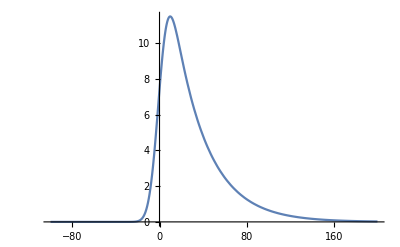

```mathematica
Plot[1/2 ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)])/.{tp->10,τ->30},{t,-100,200}]
```

```mathematica
D[1/2 ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)]),t]
```

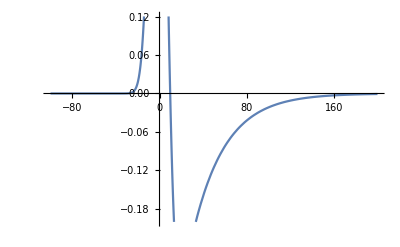

```mathematica
Plot[ⅇ^(-(t/tp-tp/(2 τ))^2+tp^2/(4 τ^2)-t/τ)-(ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)]))/(2 τ)/.{tp->10,τ->30},{t,-100,200}]
```

```mathematica
D[1/2 ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)]),{t,2}]
```

-(2 ⅇ^(-(t/tp-tp/(2 τ))^2+tp^2/(4 τ^2)-t/τ) (t/tp-tp/(2 τ)))/tp-(2 ⅇ^(-(t/tp-tp/(2 τ))^2+tp^2/(4 τ^2)-t/τ))/τ+(ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)]))/(2 τ^2)

```mathematica
Assuming[tp>0&&τ>0&&t∈Reals,Solve[ⅇ^(-(t/tp-tp/(2 τ))^2+tp^2/(4 τ^2)-t/τ)-(ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)]))/(2 τ)==0,t]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ⅇ^(-(t/tp-tp/(2 τ))^2+tp^2/(4 τ^2)-t/τ)-(ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)]))/(2 τ)==0,t]

```mathematica
Assuming[tp>0&&τ>0&&t∈Reals,Root[{ⅇ^(-(t/tp-tp/(2 τ))^2+tp^2/(4 τ^2)-t/τ)-(ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)]))/(2 τ),}]]
```

FindRoot::fdss: Search specification t should be a list with 1 to 5 elements.

FindRoot[ⅇ^(-(t/tp-tp/(2 τ))^2+tp^2/(4 τ^2)-t/τ)-(ⅇ^(tp^2/(4 τ^2)-t/τ) √π tp (1+Erf[t/tp-tp/(2 τ)]))/(2 τ),t]